A few examples of Vector fields
A vector field in R^3 that looks similar to a tornado: It would represent the velocity of an air particle at each point.

```mathematica
VectorPlot3D[{{y, -x, z}}, {x, -2, 2}, {y, -2, 2}, {z, 0, 3}, PlotTheme -> "Scientific", VectorPoints -> Coarse]
```

-Graphics3D-

The path followed by an air particle starting at (1, 1, 1).

```mathematica
Animate[Show[VectorPlot3D[{{y, -x, z}}, {x, -2, 2}, {y, -2, 2}, {z, 0, 3}, PlotTheme -> "Scientific", VectorPoints -> Coarse],ParametricPlot3D[{Cos[t] - Sin[t], Sin[t] + Cos[t], Exp[t]}, {t, 0, u}, PlotStyle -> Black],
Graphics3D[{Thick,Arrow[{{Cos[u] - Sin[u], Cos[u] + Sin[u], Exp[u]}, {Cos[u+.3] - Sin[u+.3], Cos[u+.3] + Sin[u+.3], Exp[u+.3]}}]}]
],{u,0.1,Log[3]},AnimationRunning->False]
```

A gravitational vector field :

```mathematica
VectorPlot3D[{{-x(x^2+y^2+z^2)^(-3/2),-y(x^2+y^2+z^2)^(-3/2),-z(x^2+y^2+z^2)^(-3/2)}},{x,-2,2},{y,-2,2},{z,-2,2},VectorPoints->Coarse]
```

-Graphics3D-

Another vector field that could be representing the velocity vectors on a horizontal cross section of a tornado. Here, calculating the  path of an air particle is way more difficult, but it can be done numerically in a finite interval.

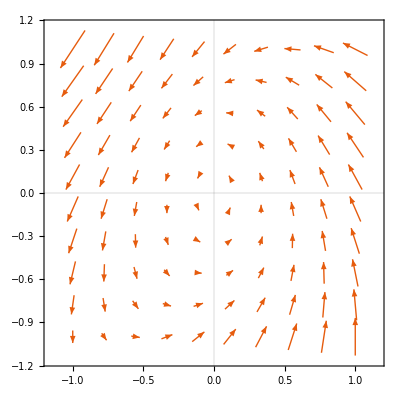

```mathematica
S4=VectorPlot[{-y-x^2,2x-y^3},{x,-1,1},{y,-1,1},VectorPoints->10,PlotTheme->"Scientific"]
```

```mathematica
Clear[s,x,y,t]
```

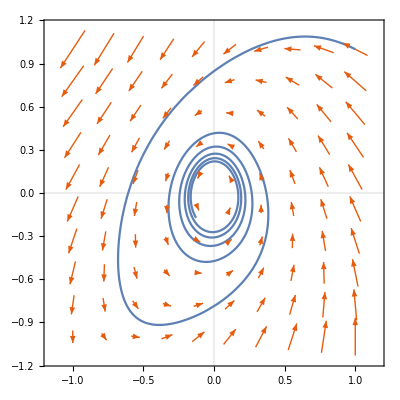

```mathematica
s=NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2 x[t]-y[t]^3,x[0]==y[0]==1},{x,y},{t,25}];
S5=ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,25}];
Show[S4,S5]
```